```mathematica
data=
Import["/Users/epersico/Google Drive/GitHub/Map Files/Resonance Widths/ResonanceWidths/ResonanceWidths/test/a_0.640000_m_3_n_5_widths.out","Table"]
```

{{0.,0.004},{0.,0.003},{0.01,0.003},{0.02,0.003},{0.03,0.003},{0.04,0.003},{0.05,0.003},{0.06,0.003},{0.07,0.003},{0.08,0.003},{0.09,0.003},{0.1,0.004},{0.11,0.004},{0.12,0.004},{0.13,0.006},{0.14,0.006},{0.15,0.008},{0.16,0.008},{0.17,0.01},{0.18,0.01},{0.19,0.012},{0.2,0.013},{0.21,0.014},{0.22,0.016},{0.23,0.018},{0.24,0.019},{0.25,0.02},{0.26,0.022},{0.27,0.024},{0.28,0.026},{0.29,0.027},{0.3,0.029},{0.31,0.031},{0.32,0.033},{0.33,0.035},{0.34,0.037},{0.35,0.04},{0.36,0.041},{0.37,0.043},{0.38,0.045},{0.39,0.046},{0.4,0.049},{0.41,0.049},{0.42,0.05},{0.43,0.053},{0.44,0.051},{0.45,0.053},{0.46,0.052},{0.47,0.052},{0.48,0.053},{0.49,0.055},{0.5,0.057},{0.51,0.059},{0.52,0.052},{0.53,0.055},{0.54,0.058},{0.55,0.061},{0.56,0.062},{0.57,0.063},{0.58,0.082},{0.59,0.088},{0.6,0.091},{0.61,0.096},{0.62,0.047}}

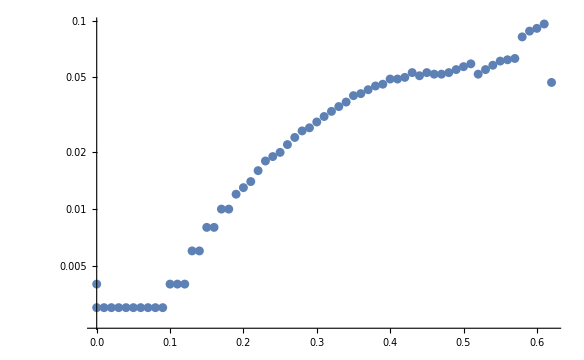

```mathematica
ListLogPlot[data]
```

```mathematica
data2=
Import["./widths/a_0.640000_m_3_n_5_widths.out","Table"];
```

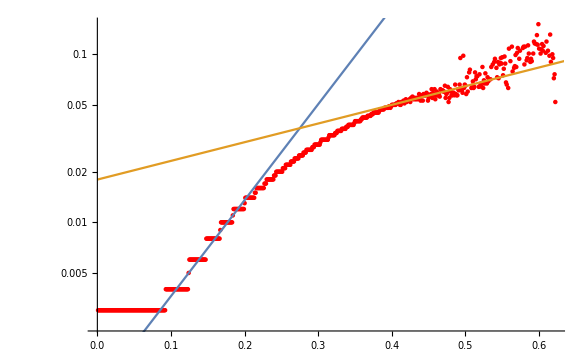

```mathematica
Show[ListLogPlot[data2,PlotStyle->Red],LogPlot[{Exp[line1],Exp[line2]},{x,0,1}]]
```

```mathematica
logdata2=data2;
logdata2[[All,2]]=Log[logdata2[[All,2]]];
```

```mathematica
line1 = Fit[logdata2[[100;;200,All]],{1,x},x]
line2 = Fit[logdata2[[420;;500,All]],{1,x},x]
```

-6.93097+13.1498 x

-4.01928+2.56005 x